```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Parameters

```mathematica
(*Approximations: complexes are in equilibrium, effectors are conserved.

 r+k <-->C

c+e ->a+e
*)
```

```mathematica
gR=1; (*NLR growth*)
gK1=10;
gK2=10;
gK3=10;
gK4=10;
gK5=10;
gK6=10;
gK={gK1,gK2,gK3,gK4,gK5,gK6};
deltaR=1; (*NLR decay*)
deltaK=1; (*kinase decay*)
(*effector-target unbinding*)
```

```mathematica
alphaF=0.5; (*R-T complex formation*)
alphaB=1; (*R-T complex unbinding*)
gamma1=0.1;  (*complex-effector binding*)
gamma2=5; (*complex-effector unbinding*)
```

```mathematica
(*note: we use Subscript[γ, 1]=0.1 to get a larger dynamic range for E*)
```

```mathematica
e0=3; (*total effector concentration*)
```

## Equations

```mathematica
(*simple approximation: Subscript[γ, 2]>>Subscript[γ, 1], so e_i-->Ei*)
```

```mathematica
getZ[kVec_,eVec_]:=Module[{thisZ},
(* return Z*)
thisTable=Table[kVec[[i]]*eVec[[i]]/(alphaB+gamma1*eVec[[i]]),{i,Length[eVec]}];
thisZ=alphaF*gamma1*Total[thisTable];
thisZ
]
```

```mathematica
drds[rVar_,aVar_,kVec_,eVec_]:=Module[{thisZ},

(*thisE=getE[rVar,tVar,e0Var];*)
thisZ=getZ[kVec,eVec];
gR-deltaR*rVar-rVar*thisZ+f[aVar]
]
```

```mathematica
dads[rVar_,aVar_,kVec_,eVec_]:=Module[{thisZ},

(*thisE=getE[rVar,tVar,e0Var];*)

thisZ=getZ[kVec,eVec];
rVar*thisZ-deltaR*aVar
]
(*dads=r[s]*t[s]*e*z;*)
```

```mathematica
(*we'll define separate k variables, but use one deriv fn*)
dkids[rVar_,aVar_,kVec_,eVec_,kIndex_]:=Module[{thisZ},

(*thisE=getE[rVar,tVar,e0Var];*)
gK[[kIndex]]-deltaK*kVec[[kIndex]]-alphaF*rVar*kVec[[kIndex]]*gamma1*eVec[[kIndex]]/(alphaB+gamma1*eVec[[kIndex]])+fk[aVar]
]
```

```mathematica
f[z_]:=z^2;(*feedback*)
```

```mathematica
fk[z_]:=0;(* kinase feedback*)
```

## solver

```mathematica
(* remove duplicates *)
processRoots[rootList_]:=Module[{cleanList,test,unique,thisDist,i,j},
cleanList={rootList[[1]]};
For[i=2,i<=Length[rootList],i++,

test=rootList[[i]];
unique=True;
For[j=1,j<=Length[cleanList],j++,
	thisDist=EuclideanDistance[test,cleanList[[j]]];
	If[thisDist<10^-5,unique=False];
];
If[unique==True,AppendTo[cleanList,test];];

];

cleanList
]
```

```mathematica
getFixedPoint[e0Var_]:=Module[{rootList,thisSol,thisGuess,guessList,cleanList,i,j,k},

guessList={0.1,1,10,100,1000};
rootList={};
Print[e0Var];
For[i=1,i<=Length[guessList],i++,
For[j=1,j<=Length[guessList],j++,
For[k=1,k<=Length[guessList],k++,

thisSol=FindRoot[{drds[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var]==0,dads[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,1]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,2]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,3]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,4]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,5]==0,dkids[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var,6]==0},{rVar,guessList[[i]],0,10^8},{k1Var,guessList[[j]],0,10^8},{k2Var,guessList[[j]],0,10^8},{k3Var,guessList[[j]],0,10^8},{k4Var,guessList[[j]],0,10^8},{k5Var,guessList[[j]],0,10^8},{k6Var,guessList[[j]],0,10^8},{aVar,guessList[[k]],0,10^8}];
residual=(drds[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var])^2+(dads[rVar,aVar,{k1Var,k2Var,k3Var,k4Var,k5Var,k6Var},e0Var])^2/.thisSol; (*check convergence*)
If[residual<=10^-6,AppendTo[rootList,{rVar,aVar,k1Var,k2Var,k3Var,k4Var,k5Var,k6Var}/.thisSol];];
];
];
];
cleanList=processRoots[rootList];
cleanList
]
```

```mathematica
(*e1 only*)
```

```mathematica
fixedPointList=Table[{{i,0,0,0,0,0},getFixedPoint[{i,0,0,0,0,0}]},{i,0,20,0.1}];
```

{0.,0,0,0,0,0}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {0.,0.100099,0.100099,0.100099,0.100099,0.100099,0.100099,99.999} is at the edge of the search region {0.,1.×10^8} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.,0.100001,0.100001,0.100001,0.100001,0.100001,0.100001,1000.} is at the edge of the search region {0.,1.×10^8} in coordinate 1 and the computed search direction points outside the region.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {0.,1.00009,1.00009,1.00009,1.00009,1.00009,1.00009,99.999} is at the edge of the search region {0.,1.×10^8} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{0.1,0,0,0,0,0}

{0.2,0,0,0,0,0}

{0.3,0,0,0,0,0}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.4,0,0,0,0,0}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.5,0,0,0,0,0}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{0.6,0,0,0,0,0}

{0.7,0,0,0,0,0}

{0.8,0,0,0,0,0}

{0.9,0,0,0,0,0}

{1.,0,0,0,0,0}

{1.1,0,0,0,0,0}

{1.2,0,0,0,0,0}

{1.3,0,0,0,0,0}

{1.4,0,0,0,0,0}

{1.5,0,0,0,0,0}

{1.6,0,0,0,0,0}

{1.7,0,0,0,0,0}

{1.8,0,0,0,0,0}

{1.9,0,0,0,0,0}

{2.,0,0,0,0,0}

{2.1,0,0,0,0,0}

{2.2,0,0,0,0,0}

{2.3,0,0,0,0,0}

{2.4,0,0,0,0,0}

{2.5,0,0,0,0,0}

{2.6,0,0,0,0,0}

{2.7,0,0,0,0,0}

{2.8,0,0,0,0,0}

{2.9,0,0,0,0,0}

{3.,0,0,0,0,0}

{3.1,0,0,0,0,0}

{3.2,0,0,0,0,0}

{3.3,0,0,0,0,0}

{3.4,0,0,0,0,0}

{3.5,0,0,0,0,0}

{3.6,0,0,0,0,0}

{3.7,0,0,0,0,0}

{3.8,0,0,0,0,0}

{3.9,0,0,0,0,0}

{4.,0,0,0,0,0}

{4.1,0,0,0,0,0}

{4.2,0,0,0,0,0}

{4.3,0,0,0,0,0}

{4.4,0,0,0,0,0}

{4.5,0,0,0,0,0}

{4.6,0,0,0,0,0}

{4.7,0,0,0,0,0}

{4.8,0,0,0,0,0}

{4.9,0,0,0,0,0}

{5.,0,0,0,0,0}

{5.1,0,0,0,0,0}

{5.2,0,0,0,0,0}

{5.3,0,0,0,0,0}

{5.4,0,0,0,0,0}

{5.5,0,0,0,0,0}

{5.6,0,0,0,0,0}

{5.7,0,0,0,0,0}

{5.8,0,0,0,0,0}

{5.9,0,0,0,0,0}

{6.,0,0,0,0,0}

{6.1,0,0,0,0,0}

{6.2,0,0,0,0,0}

{6.3,0,0,0,0,0}

{6.4,0,0,0,0,0}

{6.5,0,0,0,0,0}

{6.6,0,0,0,0,0}

{6.7,0,0,0,0,0}

{6.8,0,0,0,0,0}

{6.9,0,0,0,0,0}

{7.,0,0,0,0,0}

{7.1,0,0,0,0,0}

{7.2,0,0,0,0,0}

{7.3,0,0,0,0,0}

{7.4,0,0,0,0,0}

{7.5,0,0,0,0,0}

{7.6,0,0,0,0,0}

{7.7,0,0,0,0,0}

{7.8,0,0,0,0,0}

{7.9,0,0,0,0,0}

{8.,0,0,0,0,0}

{8.1,0,0,0,0,0}

{8.2,0,0,0,0,0}

{8.3,0,0,0,0,0}

{8.4,0,0,0,0,0}

{8.5,0,0,0,0,0}

{8.6,0,0,0,0,0}

{8.7,0,0,0,0,0}

{8.8,0,0,0,0,0}

{8.9,0,0,0,0,0}

{9.,0,0,0,0,0}

{9.1,0,0,0,0,0}

{9.2,0,0,0,0,0}

{9.3,0,0,0,0,0}

{9.4,0,0,0,0,0}

{9.5,0,0,0,0,0}

{9.6,0,0,0,0,0}

{9.7,0,0,0,0,0}

{9.8,0,0,0,0,0}

{9.9,0,0,0,0,0}

{10.,0,0,0,0,0}

{10.1,0,0,0,0,0}

{10.2,0,0,0,0,0}

{10.3,0,0,0,0,0}

{10.4,0,0,0,0,0}

{10.5,0,0,0,0,0}

{10.6,0,0,0,0,0}

{10.7,0,0,0,0,0}

{10.8,0,0,0,0,0}

{10.9,0,0,0,0,0}

{11.,0,0,0,0,0}

{11.1,0,0,0,0,0}

{11.2,0,0,0,0,0}

{11.3,0,0,0,0,0}

{11.4,0,0,0,0,0}

{11.5,0,0,0,0,0}

{11.6,0,0,0,0,0}

{11.7,0,0,0,0,0}

{11.8,0,0,0,0,0}

{11.9,0,0,0,0,0}

{12.,0,0,0,0,0}

{12.1,0,0,0,0,0}

{12.2,0,0,0,0,0}

{12.3,0,0,0,0,0}

{12.4,0,0,0,0,0}

{12.5,0,0,0,0,0}

{12.6,0,0,0,0,0}

{12.7,0,0,0,0,0}

{12.8,0,0,0,0,0}

{12.9,0,0,0,0,0}

{13.,0,0,0,0,0}

{13.1,0,0,0,0,0}

{13.2,0,0,0,0,0}

{13.3,0,0,0,0,0}

{13.4,0,0,0,0,0}

{13.5,0,0,0,0,0}

{13.6,0,0,0,0,0}

{13.7,0,0,0,0,0}

{13.8,0,0,0,0,0}

{13.9,0,0,0,0,0}

{14.,0,0,0,0,0}

{14.1,0,0,0,0,0}

{14.2,0,0,0,0,0}

{14.3,0,0,0,0,0}

{14.4,0,0,0,0,0}

{14.5,0,0,0,0,0}

{14.6,0,0,0,0,0}

{14.7,0,0,0,0,0}

{14.8,0,0,0,0,0}

{14.9,0,0,0,0,0}

{15.,0,0,0,0,0}

{15.1,0,0,0,0,0}

{15.2,0,0,0,0,0}

{15.3,0,0,0,0,0}

{15.4,0,0,0,0,0}

{15.5,0,0,0,0,0}

{15.6,0,0,0,0,0}

{15.7,0,0,0,0,0}

{15.8,0,0,0,0,0}

{15.9,0,0,0,0,0}

{16.,0,0,0,0,0}

{16.1,0,0,0,0,0}

{16.2,0,0,0,0,0}

{16.3,0,0,0,0,0}

{16.4,0,0,0,0,0}

{16.5,0,0,0,0,0}

{16.6,0,0,0,0,0}

{16.7,0,0,0,0,0}

{16.8,0,0,0,0,0}

{16.9,0,0,0,0,0}

{17.,0,0,0,0,0}

{17.1,0,0,0,0,0}

{17.2,0,0,0,0,0}

{17.3,0,0,0,0,0}

{17.4,0,0,0,0,0}

{17.5,0,0,0,0,0}

{17.6,0,0,0,0,0}

{17.7,0,0,0,0,0}

{17.8,0,0,0,0,0}

{17.9,0,0,0,0,0}

{18.,0,0,0,0,0}

{18.1,0,0,0,0,0}

{18.2,0,0,0,0,0}

{18.3,0,0,0,0,0}

{18.4,0,0,0,0,0}

{18.5,0,0,0,0,0}

{18.6,0,0,0,0,0}

{18.7,0,0,0,0,0}

{18.8,0,0,0,0,0}

{18.9,0,0,0,0,0}

{19.,0,0,0,0,0}

{19.1,0,0,0,0,0}

{19.2,0,0,0,0,0}

{19.3,0,0,0,0,0}

{19.4,0,0,0,0,0}

{19.5,0,0,0,0,0}

{19.6,0,0,0,0,0}

{19.7,0,0,0,0,0}

{19.8,0,0,0,0,0}

{19.9,0,0,0,0,0}

{20.,0,0,0,0,0}

```mathematica
(*try fixing total amount of E in each step, but distributing it evenly*)
```

```mathematica
(*fixedPointList=Table[{{i/6,i/6,i/6,i/6,i/6,i/6},getFixedPoint[{i/6,i/6,i/6,i/6,i/6,i/6}]},{i,0,20,0.1}];*)
```

```mathematica
(*try fixing total amount of E in each step, but distributing it unevenly*)
```

```mathematica
(*maxE=(1/6)//N;
otherE=(1-maxE)/5;*)
```

```mathematica
(*fixedPointList=Table[{{maxE*i,otherE*i,otherE*i,otherE*i,otherE*i,otherE*i},getFixedPoint[{maxE*i,otherE*i,otherE*i,otherE*i,otherE*i,otherE*i}]},{i,0,10,0.02}];*)
```

```mathematica
(*one or two kinases*)
```

```mathematica
(*fixedPointList=Table[{{i,0,0,0,0,0},getFixedPoint[{i,0,0,0,0,0}]},{i,0,20,0.1}];*)
```

```mathematica
(*(e,list of fixed points)*)
(*fixedPointList=Table[{{i,i,0,0,0,0},getFixedPoint[{i,i,0,0,0,0}]},{i,0,20,0.1}];*)
```

```mathematica
(*convert a list where each e has a 3D ss, to coordinates for plotting. want r*(e), t*(e), a*(e)*)
getPlottingCoords[fixedPoints_]:=Module[{rPoints,aPoints,k1Points,k2Points,k3Points,k4Points,k5Points,k6Points},

rPoints={};
aPoints={};
k1Points={};
k2Points={};
k3Points={};
k4Points={};
k5Points={};
k6Points={};

For[i=1,i<=Length[fixedPoints],i++,

thisPoint=fixedPoints[[i]];
eValue=thisPoint[[1,1]]; (*just use Subscript[E, 1] for now*)

For[j=1,j<=Length[thisPoint[[2]]],j++,

thisFixedPoint=thisPoint[[2,j]];
AppendTo[rPoints,{eValue,thisFixedPoint[[1]]}];
AppendTo[aPoints,{eValue,thisFixedPoint[[2]]}];
AppendTo[k1Points,{eValue,thisFixedPoint[[3]]}];
AppendTo[k2Points,{eValue,thisFixedPoint[[4]]}];
AppendTo[k3Points,{eValue,thisFixedPoint[[5]]}];
AppendTo[k4Points,{eValue,thisFixedPoint[[6]]}];
AppendTo[k5Points,{eValue,thisFixedPoint[[7]]}];
AppendTo[k6Points,{eValue,thisFixedPoint[[8]]}];
];
];

{rPoints,aPoints,k1Points,k2Points,k3Points,k4Points,k5Points,k6Points}

]
```

```mathematica
{rCoords,aCoords,k1Coords,k2Coords,k3Coords,k4Coords,k5Coords,k6Coords}=getPlottingCoords[fixedPointList];
```

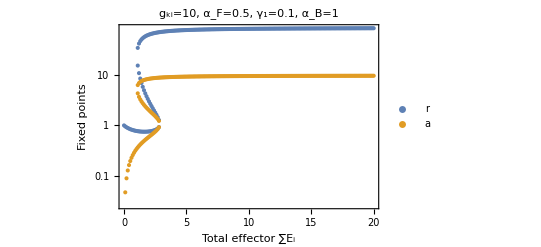

```mathematica
ListLogPlot[{rCoords,aCoords},PlotRange->{Automatic,Automatic},PlotLabel->"g_ki="<>ToString[gK1]<>", α_F="<>ToString[alphaF]<>", γ_1="<>ToString[gamma1]<>", α_B="<>ToString[alphaB](*<>"\nE_1="<>ToString[maxE]<>"E_T"*),PlotLegends->{"r","a"},FrameLabel->{"Total effector ∑E_i","Fixed points"},LabelStyle->Directive[Black, 15],Frame->{True,True,False,False}]
```

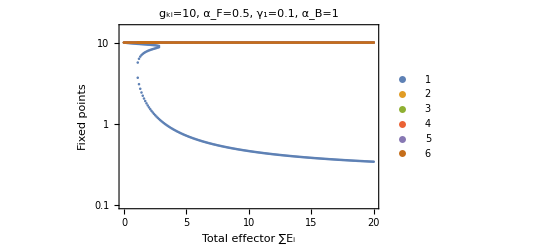

```mathematica
ListLogPlot[{k1Coords,k2Coords,k3Coords,k4Coords,k5Coords,k6Coords},PlotRange->{Automatic,{.1,15}},PlotLabel->"g_ki="<>ToString[gK1]<>", α_F="<>ToString[alphaF]<>", γ_1="<>ToString[gamma1]<>", α_B="<>ToString[alphaB](*<>"\nE_1="<>ToString[maxE]<>"E_T"*),PlotLegends->{"1","2","3","4","5","6"},FrameLabel->{"Total effector ∑E_i","Fixed points"},LabelStyle->Directive[Black, 15],Frame->{True,True,False,False}]
```

```mathematica
(*Export["zar1_balanceTest_eMax_"<>ToString[eMax]<>"_ra.mx",{rCoords,aCoords}];*)
```

```mathematica
Export["zar1Points_nodecay_nk_6.mx",rCoords]
```

zar1Points_nodecay_nk_6.mx